```mathematica
especies= 15;
metabolitos= 22;
```

```mathematica
n=especies;
m=metabolitos;
```

```mathematica
H = Table[RandomReal[{0.1,1}],m];
μ = Table[RandomReal[{0.01,0.1}],m];
δ = Table[RandomReal[{0.01,0.1}],n];
S = Table[RandomReal[5],m];
ciC = Table[RandomReal[5],m];
ciX = Table[RandomReal[5],n];
```

```mathematica
V = {
	{0,0,0,0,0,0,0,0,0,RandomReal[1],0,RandomReal[1],RandomReal[1],0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,0,RandomReal[1],0,0,0,0,0,RandomReal[1],0,0,0,0,0},
	{0,0,RandomReal[1],0,0,0,RandomReal[1],RandomReal[1],RandomReal[1],0,0,0,RandomReal[1],RandomReal[1],0},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,RandomReal[1],RandomReal[1],0,0},
	{0,0,0,0,0,0,0,0,RandomReal[1],0,0,0,0,RandomReal[1],0},
	{0,0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,RandomReal[1],0,RandomReal[1],0,0,0},
	{0,0,0,RandomReal[1],0,0,0,0,0,RandomReal[1],0,0,0,0,0},
	{RandomReal[1],0,0,0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,RandomReal[1],0,0,0,0,0,RandomReal[1],0,0,0,0,RandomReal[1],0},
	{0,0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,0,RandomReal[1]},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,0,0,RandomReal[1],RandomReal[1],0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0,0},
	{0,0,0,0,0,0,RandomReal[1],RandomReal[1],RandomReal[1],0,RandomReal[1],0,0,RandomReal[1],0},
	{0,0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,0,0},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,0,RandomReal[1],RandomReal[1],0,0,0,0,0,0,0,0,0,0},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0}
	};
W = {
	{RandomReal[1],0,RandomReal[1],RandomReal[1],0,0,RandomReal[1],RandomReal[1],RandomReal[1],0,RandomReal[1],0,0,RandomReal[1],RandomReal[1]},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,RandomReal[1],0,0,0,0,RandomReal[1],RandomReal[1],RandomReal[1],0,RandomReal[1],0,RandomReal[1],RandomReal[1],0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,RandomReal[1],RandomReal[1],0,0,0,0,0,RandomReal[1],0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,RandomReal[1],0,0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{RandomReal[1],0,RandomReal[1],0,0,0,RandomReal[1],RandomReal[1],RandomReal[1],0,0,0,RandomReal[1],RandomReal[1],0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0,0},
	{0,0,0,0,RandomReal[1],RandomReal[1],0,0,0,0,RandomReal[1],RandomReal[1],RandomReal[1],RandomReal[1],0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,RandomReal[1],RandomReal[1],RandomReal[1]},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
};
```

```mathematica
V//MatrixForm;
```

```mathematica
W//MatrixForm;
```

```mathematica
concentrationsGen[N_]:=
	Module[{X,i},
		X[t_] = {};
		For[i=1,i≤ N,i++,
			X[t_] = AppendTo[X[t],ToExpression["c"<>ToString[i[t]]]]
		];
	Return[X[t]]
	]
```

```mathematica
speciesGen[N_]:=
	Module[{X,i},
		X[t_] = {};
		For[i=1,i≤ N,i++,
			X[t_] = AppendTo[X[t],ToExpression["x"<>ToString[i[t]]]]
		];
	Return[X[t]]
	]
```

```mathematica
G[c_, v_] := v.c
```

```mathematica
R[i_]:= (c[t]⟦i⟧)/(H⟦i⟧+c[t]⟦i⟧)
```

```mathematica
c[t_]=concentrationsGen[m];
x[t_] = speciesGen[n];
```

```mathematica
vars[t_]=Flatten[{c[t],x[t]}];
```

```mathematica
g =Table[ G[V⟦;;,i⟧,c[t]],{i,1,n}];
```

```mathematica
μμ= DiagonalMatrix[μ];
```

```mathematica
δδ=DiagonalMatrix[δ];
```

```mathematica
gg =DiagonalMatrix[g];
```

```mathematica
ttdiag=DiagonalMatrix[tt];
```

```mathematica
tt=(V-W).x[t];
```

```mathematica
rr=Table[S⟦i⟧/tt⟦i⟧,{i,1,m}];
```

```mathematica
rrdiag=DiagonalMatrix[rr];
```

```mathematica
μc= μμ.c[t];
```

```mathematica
gδ=gg-δδ;
```

```mathematica
Wxr=(W.x[t]).rrdiag;
```

```mathematica
Vxr=(V.x[t]).rrdiag;
```

```mathematica
xgδ=x[t].gδ;
```

```mathematica
eqC = Table[c'[t]⟦i⟧==S⟦i⟧ +Wxr⟦i⟧-Vxr⟦i⟧-(μc⟦i⟧),{i,1,Length[c[t]]}];
eqX = Table[x'[t]⟦i⟧==xgδ⟦i⟧,{i,1,Length[x[t]]}];
cisC = Table[c[0]⟦i⟧==ciC⟦i⟧,{i,1,Length[c[t]]}];
cisX = Table[x[0]⟦i⟧==ciX⟦i⟧,{i,1,Length[x[t]]}];
```

```mathematica
sistema = Flatten[{eqC,eqX,cisX,cisC}];
```

```mathematica
sol=NDSolve[sistema,vars[t],{t,0,2000}];
```

```mathematica
varc[t_]=Flatten[{c[t]}];
varx[t_] =Flatten[{x[t]}];
```

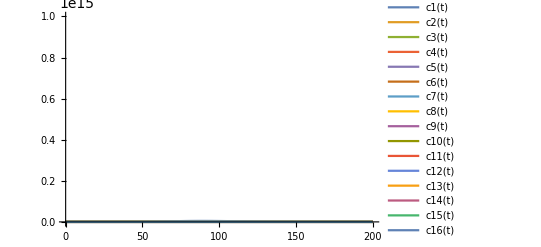

```mathematica
Plot[Evaluate[vars[t]/.sol],{t,0,200},PlotLegends->vars[t]]
```

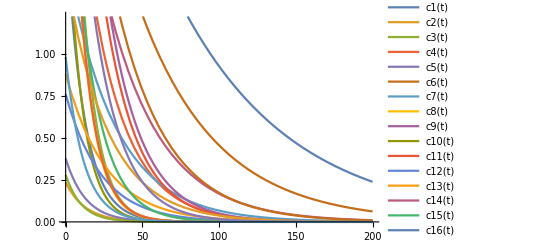

```mathematica
Plot[Evaluate[varc[t]/.sol],{t,0,200},PlotLegends->vars[t]]
```

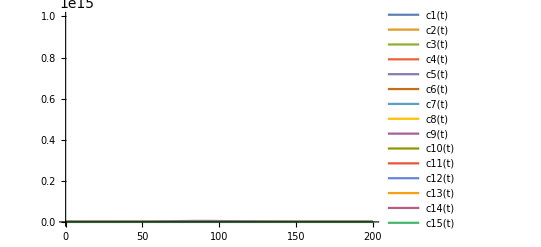

```mathematica
Plot[Evaluate[varx[t]/.sol],{t,0,200},PlotLegends->vars[t]]
```

```mathematica
rr//MatrixForm
```

(2.43687/(-0.146261 x1[t]+0.92696 x10[t]-0.0010682 x11[t]+0.676634 x12[t]+0.108965 x13[t]-0.37236 x14[t]-0.00424399 x15[t]-0.0471492 x3[t]-0.7636 x4[t]-0.437526 x7[t]-0.682297 x8[t]-0.287791 x9[t])
3.74302/(-0.0741658 x13[t]-0.120227 x3[t])
1.41201/(0.797849 x13[t]+0.538154 x3[t])
4.17176/(0.879766 x10[t]-0.0383356 x11[t]-0.998472 x13[t]-0.237808 x14[t]-0.334192 x2[t]+0.848802 x4[t]-0.606905 x7[t]-0.344646 x8[t]-0.510011 x9[t])
1.36532/(0.473816 x13[t]+0.755914 x14[t]+0.137074 x3[t]+0.91447 x7[t]+0.420047 x8[t]+0.401707 x9[t])
0.126578/(0.123442 x12[t]+0.514986 x13[t]-0.9022 x14[t]+0.27029 x3[t]-0.0879129 x7[t]-0.995739 x8[t])
3.06827/(0.00453225 x14[t]+0.608126 x9[t])
9.93359/x4[t]
1.304/(0.118622 x10[t]+0.0786853 x12[t]-0.732495 x13[t])
2.2757/(0.633778 x10[t]-0.425075 x13[t]-0.57814 x2[t]+0.295415 x4[t])
1.89819/(0.906855 x1[t]+0.514669 x13[t])
0.0369217/(0.975479 x14[t]+0.281651 x3[t]+0.14643 x9[t])
4.32414/(-0.738995 x1[t]-0.935119 x13[t]-0.337186 x14[t]+0.911072 x15[t]-0.0354646 x3[t]+0.290298 x4[t]-0.0183476 x7[t]-0.0359554 x8[t]-0.863998 x9[t])
4.94249/(0.982592 x13[t]+0.573352 x3[t])
1.73167/(-0.728515 x12[t]-0.383577 x2[t]+0.505618 x5[t]+0.640217 x6[t])
2.03675/(-0.66535 x11[t]-0.120351 x12[t]-0.0442867 x13[t]-0.924301 x14[t]-0.78237 x5[t]-0.159924 x6[t])
4.40864/(0.822007 x12[t]+0.0777604 x2[t])
4.67061/(0.959362 x11[t]+0.468837 x14[t]+0.927582 x7[t]+0.128606 x8[t]+0.0695961 x9[t])
0.185256/(-0.468373 x13[t]-0.783609 x14[t]-0.75855 x15[t]+0.327474 x4[t])
2.99158/(0.44125 x13[t]+0.63797 x3[t])
4.04305/(0.337522 x4[t]+0.780412 x5[t])
1.28511/(0.354632 x13[t]+0.744169 x3[t]))

```mathematica
tt//MatrixForm
```

(-0.146261 x1[t]+0.92696 x10[t]-0.0010682 x11[t]+0.676634 x12[t]+0.108965 x13[t]-0.37236 x14[t]-0.00424399 x15[t]-0.0471492 x3[t]-0.7636 x4[t]-0.437526 x7[t]-0.682297 x8[t]-0.287791 x9[t]
-0.0741658 x13[t]-0.120227 x3[t]
0.797849 x13[t]+0.538154 x3[t]
0.879766 x10[t]-0.0383356 x11[t]-0.998472 x13[t]-0.237808 x14[t]-0.334192 x2[t]+0.848802 x4[t]-0.606905 x7[t]-0.344646 x8[t]-0.510011 x9[t]
0.473816 x13[t]+0.755914 x14[t]+0.137074 x3[t]+0.91447 x7[t]+0.420047 x8[t]+0.401707 x9[t]
0.123442 x12[t]+0.514986 x13[t]-0.9022 x14[t]+0.27029 x3[t]-0.0879129 x7[t]-0.995739 x8[t]
0.00453225 x14[t]+0.608126 x9[t]
0.383116 x4[t]
0.118622 x10[t]+0.0786853 x12[t]-0.732495 x13[t]
0.633778 x10[t]-0.425075 x13[t]-0.57814 x2[t]+0.295415 x4[t]
0.906855 x1[t]+0.514669 x13[t]
0.975479 x14[t]+0.281651 x3[t]+0.14643 x9[t]
-0.738995 x1[t]-0.935119 x13[t]-0.337186 x14[t]+0.911072 x15[t]-0.0354646 x3[t]+0.290298 x4[t]-0.0183476 x7[t]-0.0359554 x8[t]-0.863998 x9[t]
0.982592 x13[t]+0.573352 x3[t]
-0.728515 x12[t]-0.383577 x2[t]+0.505618 x5[t]+0.640217 x6[t]
-0.66535 x11[t]-0.120351 x12[t]-0.0442867 x13[t]-0.924301 x14[t]-0.78237 x5[t]-0.159924 x6[t]
0.822007 x12[t]+0.0777604 x2[t]
0.959362 x11[t]+0.468837 x14[t]+0.927582 x7[t]+0.128606 x8[t]+0.0695961 x9[t]
-0.468373 x13[t]-0.783609 x14[t]-0.75855 x15[t]+0.327474 x4[t]
0.44125 x13[t]+0.63797 x3[t]
0.337522 x4[t]+0.780412 x5[t]
0.354632 x13[t]+0.744169 x3[t])